```mathematica
FF[A_] =FullSimplify[1/2Sum[σ E^(- I ω σ  + I E^(I β σ A)),{σ,-1,1,2}],{β,ω, A} ϵ Reals]
```

(-ⅈ Cos[Cos[A β]]+Sin[Cos[A β]]) Sin[ω-ⅈ Sin[A β]]

```mathematica
(* this substitution compotes the Fourier integral over unit circle *)
```

```mathematica
subInt[r_, l_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==I r,l][[1]])}
```

{ⅇ^X_ F_:>(F/.Solve[∂_ω X==ⅈ r,l]⟦1⟧)}

```mathematica
(* This is a binomial expansion of the power of the cosine, to use above substitution rule*)
```

```mathematica
II =1/2FullSimplify[TrigToExp[Cos[ω]^(N-2)(1-Cos[2 ω])]/.(ⅇ^(-ⅈ ω)+ⅇ^(ⅈ ω))^(-2+N) -> Binomial[N-2,l] E^(I ω (N-2-l) - I ω l) ]//Expand
```

-2^-N ⅇ^(-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]+2^(1-N) ⅇ^(2 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]-2^-N ⅇ^(4 ⅈ ω-ⅈ (4+2 l-N) ω) Binomial[-2+N,l]

```mathematica
JJ = II/.subInt[-q r, l]
```

-2^-N Binomial[-2+N,1/2 (-4+N+q r)]+2^(1-N) Binomial[-2+N,1/2 (-2+N+q r)]-2^-N Binomial[-2+N,1/2 (N+q r)]

```mathematica
(* this is to help silly Mathematica simplify sum of binomials*)
```

```mathematica
KK = Binomial[-2+N,1/2 (-2+N+q r)] FullSimplify[JJ/Binomial[-2+N,1/2 (-2+N+q r)]]
```

(2^(2-N) (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N+q r)])/(N^2-q^2 r^2)

```mathematica
(* this time it simplifies without human intervention*)
```

```mathematica
F2[β_,q_, r_, N_]  =N(N-1)/(2 * 16)(2^(2-N) (N-q^2 r^2) Binomial[-2+N,1/2 (-2+N+q r)])/(N^2-q^2 r^2)//FullSimplify
```

(2^(-5-N) (N-q^2 r^2) Gamma[1+N])/(Gamma[1/2 (2+N-q r)] Gamma[1/2 (2+N+q r)])

```mathematica
FullSimplify /@ Asymptotic[F2[β,q, z Sqrt[N]/q, N],{N , Infinity,2}]
```

-(ⅇ^(-z^2/2) √N (-1+z^2))/(16 √(2 π))+(ⅇ^(-z^2/2) (-1+z^2) (3-6 z^2+z^4))/(192 √N √(2 π))-(ⅇ^(-z^2/2) (-1+z) (1+z) (45-660 z^2+570 z^4-108 z^6+5 z^8))/(23040 N^(3/2) √(2 π))

```mathematica
EE =1/2 Integrate[(√N)/(16 √(2 π)) N^3/(3 *3 Zeta[3])E^(-μ N),{N,0, Infinity}, GenerateConditions->False]
```

35/(1536 √2 μ^(9/2) Zeta[3])

```mathematica
Zlim =Asymptotic[ Binomial[N,N/2]2^(-N) N^2/( 2 Zeta[2]),N->Infinity]
```

(3 √2 N^(3/2))/π^(5/2)

```mathematica
ZZ =1/2 Integrate[Zlim  E^(- μ N),{N,0,Infinity}, GenerateConditions->False]
```

9/(4 √2 π^2 μ^(5/2))

```mathematica
(* result for r=0 contributrion to the enstrophy*)
result = EE/ZZ
```

(35 π^2)/(3456 μ^2 Zeta[3])

```mathematica
N[(35 π^2)/(3456 μ^2 Zeta[3]),10]
```

0.08315129725/μ^2

```mathematica
(* now the hard part-- averaging over the Euler ensemble *)
```

```mathematica
SumP[F_, q_,r_, M_]:= 
Block[{betas, ints},
betas = N[Select[Range[q-1],GCD[#,q]==1&]2 Pi/q,20];
ints =  F[#,q r, M]& /@ betas;
(Plus @@  ints)
];
```

```mathematica
EulerSum[F_, M_] := Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)SumP[F,q,r,M]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}];
```

```mathematica
PartitionFunction[M_]:=
PartitionFunction[M]=
Sum[Sum[If[OddQ[M+ q r],0,Binomial[M,(M+q r)/2]2^(-M)EulerPhi[q]],{r,-Floor[M/q],Floor[M/q]}],{q,2 + Mod[M,2],M-2}]
```

```mathematica
EulerAverage[F_, M_] := EulerSum[F,M]/PartitionFunction[M];
```

```mathematica
EulerAverage[F2, 1000]
```

118.86270222802318

```mathematica
(* this takes a few minutes or half an hour, depending of number of cores*)
```

```mathematica
ParallelTable[PartitionFunction[M],{M,3,1000}];
```

```mathematica
F2data = ParallelTable[EulerAverage[F2,M],{M,4,1000}];
```

```mathematica
F2data[[;;2]] (* garbage, too low M*)
```

{0.,-0.003255208333333333333}

```mathematica
f2test=Take[Transpose[{Range[4,1000],F2data}],{3,-1,2}];
```

```mathematica
f2test[[1]]
```

{6,0.00698355741279069767}

```mathematica
Dimensions[f2test]
```

{498,2}

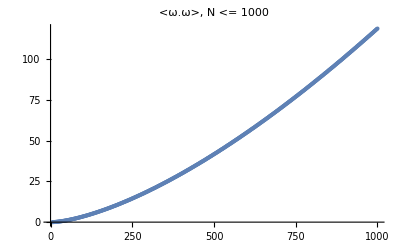

```mathematica
ListPlot[f2test,PlotLabel->"<ω.ω>, N <= 1000"]
```

```mathematica
f2test[[10]]
```

{24,0.317981016022237209}

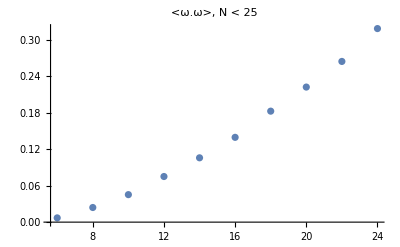

```mathematica
ListPlot[f2test[[;;10]],PlotLabel->"<ω.ω>, N < 25"]
```

```mathematica
f2model = LinearModelFit[Log[f2test[[-200;;]]],{x},x]
```

FittedModel[-«59»+«59» x]

```mathematica
Normal[f2model]
```

-5.6556773224669291+1.5105218612351004 x

```mathematica
f2meanmodel = NonlinearModelFit[Log[f2test[[-200;;]]],{a + b Log[x]+ 1.5 x},{a, b},x]
```

FittedModel[«1»]

```mathematica
Normal[f2meanmodel]
```

-5.71855+1.5 x+0.070124 Log[x]

```mathematica
ShowLogFitModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[model[x],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{model[Log[N]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"Log[N]", "Log[<ω.ω>]"}
];
```

```mathematica
ShowFitLogModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{Exp[model[Log[N]]]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<ω.ω>"}
];
```

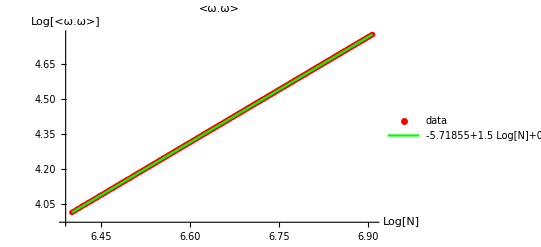

```mathematica
ShowLogFitModel[Log[f2test[[-200;;]]],f2meanmodel,"<ω.ω>"]
```

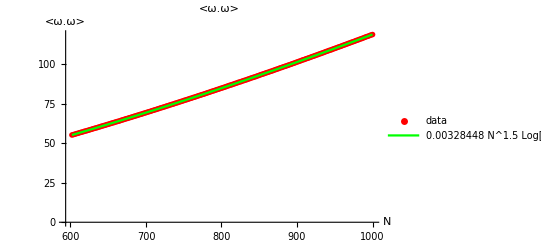

```mathematica
ShowFitLogModel[f2test[[-200;;]],f2meanmodel,"<ω.ω>"]
```

```mathematica
f2meanmodel["ParameterTable"]
```

General::munfl: Exp[-1059.1] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -5.71855 | 0.00195984 | -2917.87 | 0.
b | 0.070124 | 0.00103242 | 67.9219 | 3.86518×10^-139

```mathematica
Exp[f2meanmodel[Log[N]]]
```

0.00328448 N^1.5 Log[N]^0.070124